# 12 Conditioning

We want to be able to estimate what effect small changes in input have on the output in linear algebra problems

Algorithmic implementations always have clear input and output.

Some algorithms have more than one input and/or more than one output.

Since our inputs are vectors and/or matrices there are a variety of ways to measure the perturbation size.

Stability concerns perturbations of the input of an algorithmic implementation. This includes floating point arithmetic!

In an appropriate sense, small input changes produce small output changes for a stable algorithm.

Sometimes it is easier to think of a problem very abstractly as a function f:X→Y

As before some of these functions will have more than one input and/or more than one output. We lump all the inputs together as X  and all the outputs together as Y.

There are various possible measures for perturbation size.

Conditioning concerns perturbations of the input of an abstract function.

The function f is well conditioned at a point x^*∈X if small perturbations in x^* give small perturbations in f(x^*).

An ill-conditioned problem produces large perturbations in f(x^*) for some small perturbation in x^*.

It is possible to have an unstable algorithm for a well-conditioned problem!

## Condition Number

If f is differentiable we can write J(x)=Df(x) then δf=J(x).δx and

#### Absolute Condition Number κ̂ | = | lim_(δ->0) max_(||δx||<δ) (||f(x+δx)-f(x)||)/(||δx||) | = | max_δx (||δf||)/(||δx||)=max_δx (||J(x).δx||)/(||δx||)=||J(x)(||)_induced

#### Relative Condition Number κ | = | lim_(δ->0) sup_(||δx||<δ) (||f(x+δx)-f(x)||/||f(x)||)/(||δx||/||x||) | = | sup_δx (||δf||/||f(x)||)/(||δx||/||x||)=(||J(x)(||)_ind)/(||f(x)||/||x||)

As usual we care more about precision than we do accuracy. Relative condition numbers are much more important than absolute condition numbers!

A problem is well conditioned if k is small (say less than 10^2) and badly conditioned if k is big (say bigger than 10^10).

## Condition Number of f:ℝ→ℝ

We have formulas if f is smooth
	κ̂(x)=sup_δx (||f'(x) δx||)/(||δx||)=|f'(x)|
and 
	κ(x)=sup_δx (||f'(x) δx||/||f(x)||)/(||δx||/||x||)=|f'(x)|×(|x|)/(|f(x)|)

## Condition Number of f:ℝ^n→ℝ^m

We have formulas if f is smooth and we use the Euclidean norms to measure perturbations in the input space ℝ^n and the output space ℝ^m.
	κ̂(x)=sup_δx (||Df(x).δx||)/(||δx||)=sup_δx (||J(x).δx||)/(||δx||)=||J(x)(||)_induced=σ_1
and 
	κ(x)=sup_δx (||Df(x) .δx||/||f(x)||)/(||δx||/||x||)=σ_1×(|x|)/(|f(x)|).

## Condition Number of x→A.x with A∈ℝ^(m×m)

This linear map is smooth. With σ_(1:m) the thick singular values of A and Euclidean norms for the input space ℝ^m and output space ℝ^m we have
	κ̂(x)=σ_1
and 
	κ(x)=σ_1×(||x||)/(||A.x||)≤σ_1×max_(||x||) (||x||)/(||A.x||)=σ_1/σ_m
The condition number of a square matrix is defined to be the ratio of the largest singular value to the smallest singular value.  For A∈ℝ^(m×m) everyone writes 
	K(A)=σ_1/σ_m.
Note if A is not invertible σ_m=0. The condition number of a non-invertible square matrix is ∞.

## Condition Number of solving A.x=b→x with A∈ℝ^(m×m)

This map is smooth with two inputs (A and b) and provided A is invertible we can write it as 
	(A,b)→x=A^-1 b	 
Again write σ_(1:m) for the thick singular values of A and of course use Euclidean norms.

The sensitivity with respect to b is similar to the earlier computation
	(κ̂)_b(A,b)=max(1/σ_(1:m))=1/σ_m
and 
	κ_b(A,b)=1/σ_m×(||b||)/(||A^-1.b||)≤1/σ_m×max_(||b||) (||b||)/(||A^-1.b||)=1/σ_m×1/min[1/σ_(1:m)]=1/σ_m×1/(1/σ_1)=σ_1/σ_m
This is not a typo take a look at the definition and note that 
	κ(A^-1)=κ(A).

Sensitivity with respect to A→A+δA looks slightly different.  We could start from the derivative definitions but we are going to start with the perturbed equation with a fixed b
	(A+δA).(x+δx)=b  
and expand to get
	A.x+δA.x+A.δx+δA.δx=b.
Since A.x=b we have
	  δA.x+A.δx+δA.δx=0
and since δx→0  as δA→0 the quadratic term δA.δx is negligible in the limit and 
	δA.x+A.δx≈0
or in other words 
	δx≈-A^-1.δA.x
plugging this into our definitions of condition numbers gives. 
  
	(κ̂)_A(A,b) | = | lim_(δ->0) sup_(||δA||<δ) (||(A+δA)^-1.b-A^-1.b||)/(||δA||)     
  | = | lim_(δ->0) sup_(||δA||<δ) (||((A+δA)^-1-A^-1).b||)/(||δA||)       
  | = | lim_(δ->0) sup_(||δA||<δ) (||((A+δA)^-1.(δA).A^-1).b||)/(||δA||)
  | = | lim_(δ->0) sup_(||δA||<δ) (||((A+δA)^-1.(δA)).(A^-1.b)||)/(||δA||)

```mathematica
f[x_]:=(σ+x)^-1-σ^-1
f'[0]
```

-1/σ^2

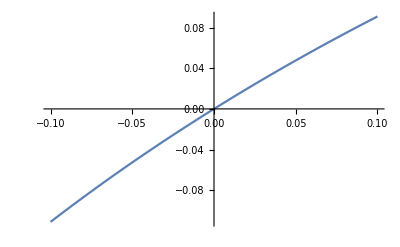

```mathematica
Plot[ x/((σ+x)σ),{x, -0.1,0.1}]
```

```mathematica
Plo
```

and 
	κ_b(A,b)=1/σ_m×(||b||)/(||A^-1.b||)≤1/σ_m×max_(||b||) (||b||)/(||A^-1.b||)=1/σ_m×1/min[1/σ_(1:m)]=1/σ_m×1/(1/σ_1)=σ_1/σ_m
This is not a typo we have
	κ(A^-1)=κ(A).

## Simple Examples

What is the relative condition number of x→sin(3x) at x=1.2?

What is the relative condition number of x→sin(3x) at x=π/3?

## Condition Number of x→y=A.x

Two bits of input (the matrix A and the vector x) one vector y of output.

## Condition Number of (A.x=b)→x

Two bits of input (the matrix A and the vector b) with one vector x  of output.

## Quadratic Equation

Discuss the conditioning of the the roots of the polynomial y^2+b y + c=0 on the coefficients b and c.